```mathematica
Σ[i_,j_]:=KroneckerProduct[PauliMatrix[i],PauliMatrix[j]]
```

```mathematica
Clear[H]
H[kx_,ky_, t0_:1,tx_:0,ty_:0.75,dy_:.75,dx_:2,sx_:2,sy_:0,bx_:0,by_:1]:=(t0 + tx Cos[kx] + ty Cos[ky])*Σ[0,3]+dy Sin[ky]*Σ[0,2] + dx Sin[kx]*Σ[3,1] + (sx Cos[kx] + sy Cos[ky])*Σ[1,1] + bx *Σ[1,0] + by*Σ[2,3]
```

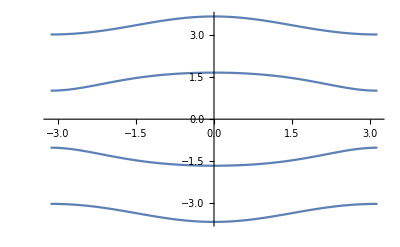

Set::shape: Lists {vals1,vecs1} and ComputeEigenstateCorner[{d0y,d1x,t00,t0y},{1,2,0.5,0.3},getRealSpaceHam[H,11,11],{}] are not the same shape.

```mathematica
Lx1=Ly1=11;

HfullMat1=getRealSpaceHam[H,Lx1,Ly1];
Manipulate[{vals1,vecs1}=Chop[ComputeEigenstateCorner[{d0y,d1x,t00,t0y},{td0y,td1x,tt00,tt0y},HfullMat1,{}]];
,
{{tt00,.5},0,2},{{td0y,1},0,2},{{tt0y,0.3},0,2},{{td1x,2},0,2}
]
Manipulate[PlotEigenstates[vals1,vecs1,num,Lx1,Ly1]
,
{{num,2 Lx1 Ly1},1,4 Lx1 Ly1 ,1}
]
Plot[Sort[Eigenvalues[H[0,ky]]],{ky,-π,π}]
```

```mathematica
Eigenvalues[H[kx,ky, t0,0,ty,ty,sx,sx,0,0,by]]//FullSimplify
```

{-√(by^2+sx^2+t0^2+ty^2+2 t0 ty Cos[ky]-√2 √(by^2 (2 (sx^2+t0^2)+ty^2+ty (4 t0 Cos[ky]+ty Cos[2 ky])))),√(by^2+sx^2+t0^2+ty^2+2 t0 ty Cos[ky]-√2 √(by^2 (2 (sx^2+t0^2)+ty^2+ty (4 t0 Cos[ky]+ty Cos[2 ky])))),-√(by^2+sx^2+t0^2+ty^2+2 t0 ty Cos[ky]+√2 √(by^2 (2 (sx^2+t0^2)+ty^2+ty (4 t0 Cos[ky]+ty Cos[2 ky])))),√(by^2+sx^2+t0^2+ty^2+2 t0 ty Cos[ky]+√2 √(by^2 (2 (sx^2+t0^2)+ty^2+ty (4 t0 Cos[ky]+ty Cos[2 ky]))))}

```mathematica
(2 (sx^2+t0^2)+ty^2+ty (4 t0 Cos[ky]+ty Cos[2 ky]))//ExpandAll//TrigExpand
```

2 sx^2+2 t0^2+ty^2+4 t0 ty Cos[ky]+ty^2 Cos[ky]^2-ty^2 Sin[ky]^2

```mathematica
Clear[Σ]

Σpp2=1/4 KroneckerProduct[PauliMatrix[0]+PauliMatrix[3],PauliMatrix[0]+PauliMatrix[3],PauliMatrix[2]];
Σpp3=1/4 KroneckerProduct[PauliMatrix[0]+PauliMatrix[3],PauliMatrix[0]+PauliMatrix[3],PauliMatrix[3]];
Σ0m3=1/2 KroneckerProduct[PauliMatrix[0],PauliMatrix[0]-PauliMatrix[3],PauliMatrix[3]];
Σ3m3=1/2 KroneckerProduct[PauliMatrix[3],PauliMatrix[0]-PauliMatrix[3],PauliMatrix[3]];
Σm20=1/2 KroneckerProduct[PauliMatrix[0]-PauliMatrix[3],PauliMatrix[2],PauliMatrix[0]];
Σ[i_,j_,k_]:=KroneckerProduct[PauliMatrix[i],PauliMatrix[j],PauliMatrix[k]]
```

```mathematica
Clear[H]
H[kx_,ky_, kz_, tx_:1,μ1_:1,μ2_:1,α1_:1,α2_:1,ty1_:1,ty2_:1,tz_:1]:=-tx*Σpp2*Sin[kx]-tx Σpp3*Cos[kx]+μ1 Σ0m3+μ2 Σ3m3 - α1 Σm20 -α2 Σ[2,0,0]+tz Σ[1,0,0] Sin[kz]+ tz Σ[2,0,0]Cos[kz]+ty1 Σ[0,1,0] Sin[ky] + ty1 Σ[0,2,0] Cos[ky]+ ty2 Σ[3,1,0] Sin[ky]+ ty2 Σ[3,2,0] Cos[ky]
```

```mathematica
L=8
```

8

```mathematica
Clear[H]
Hrs = ConstantArray[0,{L,L,L,8,L,L,L,8}];
pos = ConstantArray[0,{L,L,L,8,3}];
Do[
Hrs[[nx,ny,nz,;;,nx+1,ny,nz,;;]]+=1/2(-tx*Σpp2*ⅈ-tx Σpp3)
,{nx,L-1},{ny,L},{nz,L}]

Do[
Hrs[[nx,ny,nz,;;,nx,ny+1,nz,;;]]+=1/2(ty1 Σ[0,1,0] ⅈ + ty1 Σ[0,2,0]+ ty2 Σ[3,1,0]ⅈ+ ty2 Σ[3,2,0])
,{nx,L},{ny,L-1},{nz,L}]

Do[
Hrs[[nx,ny,nz,;;,nx,ny,nz+1,;;]]+=1/2(+tz Σ[1,0,0] ⅈ+ tz Σ[2,0,0])
,{nx,L},{ny,L},{nz,L-1}]
dims=Dimensions[Hrs];
mat=ArrayReshape[Hrs,{Times@@dims[[;;4]],Times@@dims[[5;;]]}];
mat +=mat†;
Hrs = ArrayReshape[mat,dims];
```

```mathematica
Do[
Hrs[[nx,ny,nz,;;,nx,ny,nz,;;]]+=+μ1 Σ0m3+μ2 Σ3m3 - α1 Σm20 (*-α2 Σ[2,0,0]*);
pos[[nx,ny,nz,;;]]=(lx*nx+ly*ny+lz*nz)
,{nx,L},{ny,L},{nz,L}]
```

```mathematica
mat=ArrayReshape[Hrs,{Times@@dims[[;;4]],Times@@dims[[5;;]]}];
```

```mathematica
lx={1,0,0.0};
ly={0.0,1,0.0};
lz={0.0,0.0,1};
```

```mathematica
position=ArrayReshape[Table[lx*nx+ly*ny+lz*nz+0*ns,{nx,Range[L]},{ny,Range[L]},{nz,Range[L]},{ns,8}],{L^3 8,3}];
```

```mathematica
{eval,evec}=Eigensystem[mat/.{tx->1,ty1->2,ty2->2,tz->1,α1->1,μ1->0.2,μ2->1}];
```

```mathematica
avpos=Table[(Abs[e]^2).position//Chop,{e,evec}];
```

```mathematica
IntegerQ[#]&/@{1,1,1.2}
```

{True,True,False}

```mathematica
cases=Table[Tally[IntegerQ[Rationalize[#]]&/@ap],{ap,avpos}];
```

```mathematica
evalcases={eval,cases}ᵀ;
```

```mathematica
cols={Black,Blue,Green,Red}
casecolor=Table[Switch[ec[[2]],{{False,3}},cols[[1]],{{False,2},{True,1}},cols[[2]],{{True,3}},cols[[3]],{{False,1},{True,2}},cols[[4]]],{ec,evalcases}];
```

{GrayLevel[0],RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[1, 0, 0]}

```mathematica
(Abs[evec[[-1]]]^2).position//Chop
```

{1.,1.,1.}

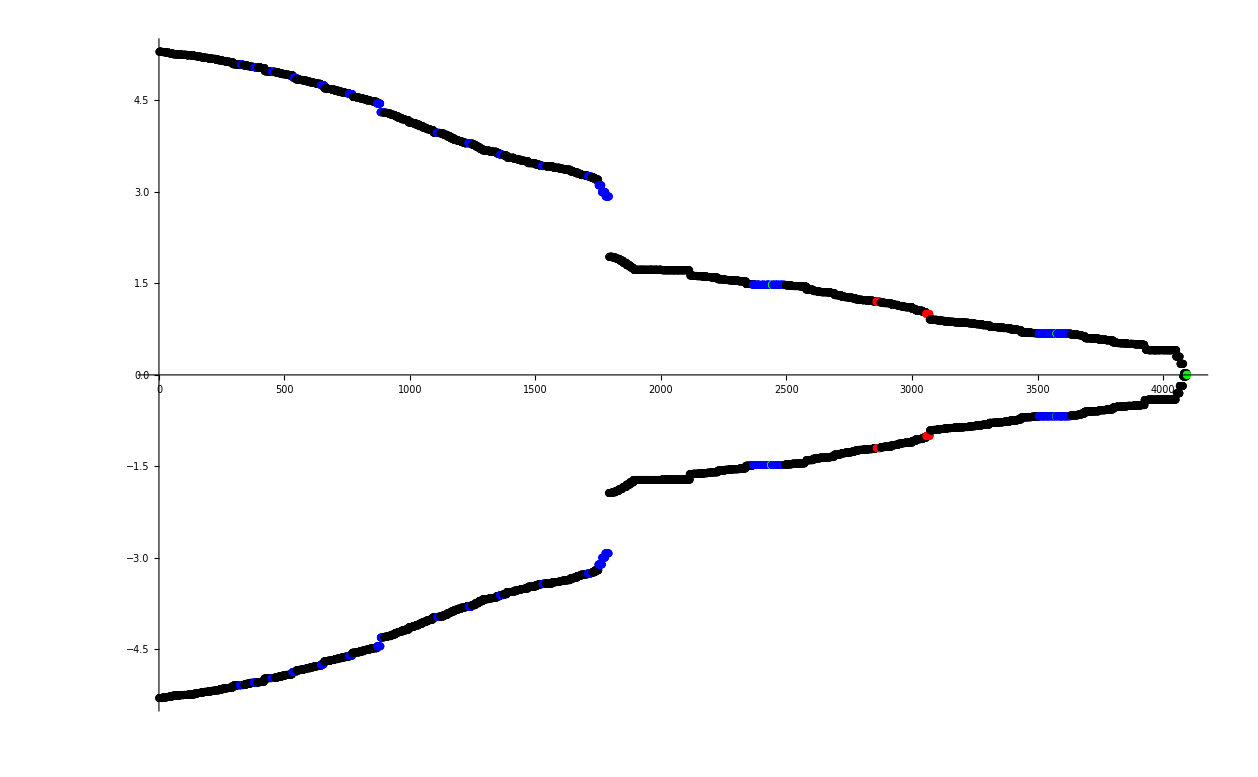

```mathematica
ListPlot[Table[{{i,eval[[i]]}},{i,Length[eval]}],PlotStyle->casecolor]
```

```mathematica
evec[[Position[casecolor,n_ /; n==cols[[3]]]//Flatten,;;]][[1]]
```

{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.560629+0. ⅈ,0.+0. ⅈ,0.+0.828067 ⅈ,0.+0. ⅈ}